```mathematica
Manipulate[
Module[{Slope,Intercept,PhaseBoundary,pureTiU2x,e1T,e2T,e1x,e2x,pureTiPoints,pureUPoints,pureTiU2Points,e1Points,e2Points,pb1Points,pb2Points,pb3Points,pb4Points,pb5Points,pb6Points,pb7Points,xfromT,Lever1Amount,Lever2Amount,GreenLever,RedLever,BlueLever,LiquidComp,RedAmount,BlueAmount,OrangeLever,GreenAmount,OrangeAmount,p1,p2},
Slope[ x1_, y1_, x2_, y2_ ] := (y2-y1)/(x2-x1);Intercept[ x1_, y1_, x2_, y2_ ] := (x1 y2-x2 y1)/(x1-x2);
PhaseBoundary[ Points_, x_ ] := (Slope[ Points[[1]],Points[[2]],Points[[3]], Points[[4]] ]*x)+ Intercept[ Points[[1]],Points[[2]], Points[[3]], Points[[4]] ];

pureTiU2x = N@2/3;

e1T=655;e2T=720;e1x=0.28;e2x=0.95;

pureTiPoints={0,882};pureUPoints={1,770};pureTiU2Points={pureTiU2x,890};

e1Points={e1x,e1T};e2Points={e2x,e2T};
pb1Points= Flatten[{pureTiPoints,e1Points}];
pb2Points=Flatten[{e1Points,pureTiU2Points}];
pb3Points=Flatten[{pureTiU2Points,e2Points}];
pb4Points=Flatten[{e2Points,pureUPoints}];
pb5Points={pureTiPoints[[1]],e1Points[[2]],pureTiU2Points[[1]],e1Points[[2]]};
pb6Points={pureTiU2Points[[1]],e2Points[[2]],pureUPoints[[1]],e2Points[[2]]};
pb7Points={pureTiU2Points[[1]],0,pureTiU2Points[[1]],pureTiU2Points[[2]]};

xfromT[Points_,T_]:=(T-Intercept[Points[[1]],Points[[2]], Points[[3]], Points[[4]] ])/Slope[ Points[[1]],Points[[2]],Points[[3]], Points[[4]] ];

Lever1Amount[ Lever1_, Lever2_ ] := (Lever2/Lever1)/(1+(Lever2/Lever1));
Lever2Amount[ Lever1_, Lever2_ ] := 1-Lever1Amount[ Lever1, Lever2 ];


p1=Show[
Plot[ PhaseBoundary[ pb1Points, x ], {x,pb1Points[[1]],pb1Points[[3]]}, 
PlotStyle-> Black, PlotRange-> {{0,1},{600,925}}, Frame->True, FrameLabel->{ Row@{"mole fraction uranium ",Subscript[Style["x",Italic],"U"]},"temperature (˚C)"},LabelStyle->{17,Black}, ImageSize->{400,400},
AspectRatio-> Full],
Plot[ PhaseBoundary[ pb2Points,x ], {x,pb2Points[[1]],pb2Points[[3]]}, PlotStyle-> Black  ],
Plot[ PhaseBoundary[ pb3Points,x ], {x,pb3Points[[1]],pb3Points[[3]]}, PlotStyle-> Black  ],
Plot[ PhaseBoundary[ pb4Points,x ], {x,pb4Points[[1]],pb4Points[[3]]}, PlotStyle-> Black  ],
Plot[ PhaseBoundary[ pb5Points,x ], {x,pb5Points[[1]],pb2Points[[3]]}, PlotStyle-> Black  ],
Plot[ PhaseBoundary[ pb6Points,x ], {x,pb6Points[[1]],pb6Points[[3]]}, PlotStyle-> Black  ],
Graphics[ Line[ { {pb7Points[[1]],pb7Points[[2]]},{pb7Points[[3]],pb7Points[[4]]} } ] ],
Graphics[{PointSize@0.025, Purple,Point[ {PointX,PointT}] } ],
Which[ 
(PointX == 0),
Show[ 
Graphics[ {PointSize@0.025,Blue,Point[ {PointX,PointT}] } ],
Graphics[ {Dotted,Thickness@0.007,Blue,Line[ {{PointX,PointT},{PointX,0}} ] } ]
 ],
(PointX == 1),
Show[ 
Graphics[ {PointSize@0.025,RGBColor[1,0.4,0],Point[ {PointX,PointT}] } ],
Graphics[ {Dotted,Thickness@0.007,RGBColor[1,0.4,0],Line[ {{PointX,PointT},{PointX, 0}} ] } ]
 ],
(PointX <  pureTiU2x),
Which[
(PointT < e1T),
Show[ 
Graphics[ {PointSize@0.025,Blue,Point[ {0,PointT}] } ],Graphics[ {PointSize@0.025,RGBColor[0,0.6,0],Point[ {pureTiU2x,PointT}] } ],
Graphics[ {Dashed,Blue,Line[ {{0,PointT},{PointX,PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007, Blue,Line[ {{0,PointT},{0,0}} ] } ],
Graphics[ {Dashed,RGBColor[0,0.6,0],Line[ {{PointX,PointT},{pureTiU2x,PointT}} ] } ], 
Graphics[ {Dotted,Thickness@0.007, RGBColor[0,0.6,0],Line[ {{pureTiU2x,PointT},{pureTiU2x,0} } ] } ]
 ],
(PointT ≥ e1T),
Which[
(PointX < e1x),
Which[
(PointX < xfromT[ pb1Points, PointT ]), 
Show[ 
Graphics[ {PointSize@0.025,Blue,Point[ {0,PointT}] } ],Graphics[ {PointSize@0.025,Magenta,Point[ { xfromT[ pb1Points, PointT ],PointT}] } ],
Graphics[ {Dashed,Blue,Line[ {{0,PointT},{PointX,PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007,Blue,Line[ {{0,PointT},{0,0}} ] } ],
Graphics[ {Dashed,Magenta,Line[ {{PointX,PointT},{ xfromT[ pb1Points, PointT ],PointT} } ] } ],
Graphics[ {Dotted,Thickness@0.007,Magenta,Line[ {{xfromT[ pb1Points, PointT ],0},{xfromT[ pb1Points, PointT ],PointT} } ] } ]
 ],
(PointX ≥ xfromT[ pb1Points, PointT ]),  
Show[ 
Graphics[ {PointSize@0.025,Purple,Point[ {PointX,PointT}] } ], 
Graphics[ {Dotted,Thickness@0.007,Magenta,Line[ {{PointX,0},{PointX,PointT} } ] } ]
 ]],
(PointX ≥ e1x),
Which[
(PointX ≥ xfromT[ pb2Points, PointT ]), 
Show[ 
Graphics[ {PointSize@0.025,Magenta,Point[  { xfromT[ pb2Points, PointT ],PointT}] } ],Graphics[ {PointSize@0.025,RGBColor[0,0.6,0],Point[{pureTiU2x, PointT}] } ], 
Graphics[ {Dashed,Magenta,Line[ {{ xfromT[ pb2Points, PointT ],PointT},{PointX,PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007,Magenta,Line[ {{xfromT[ pb2Points, PointT ],0},{xfromT[ pb2Points, PointT ],PointT} } ] } ],
Graphics[ {Dashed,RGBColor[0,0.6,0],Line[ {{PointX,PointT},{pureTiU2x, PointT} } ] } ],
Graphics[ {Dotted,Thickness@0.007,RGBColor[0,0.6,0],Line[ {{pureTiU2x, PointT},{pureTiU2x, 0} } ] } ]
 ],
(PointX < xfromT[ pb2Points, PointT ]),  
Show[ 
Graphics[ {PointSize@0.025,Purple,Point[ {PointX,PointT}] } ], 
Graphics[ {Dotted,Thickness@0.007,Magenta,Line[ {{PointX,0},{PointX,PointT} } ] } ]
 ]]]],
(PointX ≥  pureTiU2x),
Which[
(PointT < e2T),
Show[ 
Graphics[ {PointSize@0.025,RGBColor[0,0.6,0],Point[ {pureTiU2x,PointT}] } ],Graphics[ {PointSize@0.025,RGBColor[1,0.4,0],Point[ {1,PointT}] } ],
Graphics[ {Dashed,RGBColor[0,0.6,0],Line[ {{pureTiU2x,PointT},{PointX,PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007, RGBColor[0,0.6,0],Line[ {{pureTiU2x,PointT},{pureTiU2x,0}} ] } ],
Graphics[ {Dashed,RGBColor[1,0.4,0],Line[ {{PointX,PointT},{1,PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007,RGBColor[1,0.4,0],Line[ {{1,PointT},{1,0} } ] } ]
 ],
(PointT ≥ e2T),
Which[
(PointX < e2x),
Which[
(PointX < xfromT[ pb3Points, PointT ]), 
Show[ 
Graphics[ {PointSize@0.025,RGBColor[0,0.6,0],Point[ {pureTiU2x,PointT}] } ],Graphics[ {PointSize@0.025,Magenta,Point[ { xfromT[ pb3Points, PointT ],PointT}] } ], 
Graphics[ {Dashed,RGBColor[0,0.6,0],Line[ {{pureTiU2x,PointT},{PointX,PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007, RGBColor[0,0.6,0],Line[ {{pureTiU2x,PointT},{pureTiU2x,0}} ] } ],
Graphics[ {Dashed,Magenta,Line[ {{PointX,PointT},{ xfromT[ pb3Points, PointT ],PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007,Magenta,Line[ {{ xfromT[ pb3Points, PointT ],PointT},{ xfromT[ pb3Points, PointT ],0} } ] } ]
 ],
(PointX ≥ xfromT[ pb3Points, PointT ]),
Show[ 
Graphics[ {PointSize@0.025,Purple,Point[ {PointX,PointT}] } ], 
Graphics[ {Dotted,Thickness@0.007,Magenta,Line[ {{PointX,0},{PointX,PointT} } ] } ] 
]],
(PointX ≥ e2x),
Which[
(PointX ≥ xfromT[ pb4Points, PointT ]),
Show[ 
Graphics[ {PointSize@0.025,Magenta,Point[  { xfromT[ pb4Points, PointT ],PointT}] } ],Graphics[ {PointSize@0.025,RGBColor[1,0.4,0],Point[{1, PointT}] } ], 
Graphics[ {Dashed,Magenta,Line[ {{ xfromT[ pb4Points, PointT ],PointT},{PointX,PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007,Magenta,Line[ {{ xfromT[ pb4Points, PointT ],PointT},{ xfromT[ pb4Points, PointT ],0}} ] } ],
Graphics[ {Dashed,RGBColor[1,0.4,0],Line[ {{PointX,PointT},{1, PointT}} ] } ],
Graphics[ {Dotted,Thickness@0.007, RGBColor[1,0.4,0],Line[ {{1, PointT},{1,0} } ] } ]
 ],
(PointX < xfromT[ pb4Points, PointT ]),
Show[ 
Graphics[ {PointSize@0.025,Purple,Point[ {PointX,PointT}] } ], 
Graphics[ {Dotted,Thickness@0.007,Magenta,Line[ {{PointX,0},{PointX,PointT} } ] } ]
 ]]]]]];


p2=Show[ 
BarChart[
Which[ 
(PointX == 0),
(
RedAmount = 0;
BlueAmount =1;
GreenAmount =  0;
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
),
(PointX == 1), 
(
RedAmount = 0;
BlueAmount =0;
GreenAmount =  0;
OrangeAmount = 1;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
),
(PointX <  pureTiU2x),
Which[
(PointT < e1T), 
(
BlueLever = Abs[ 0-PointX ];
GreenLever = Abs[ PointX-pureTiU2x  ];
RedAmount = 0;
BlueAmount = Lever1Amount[ BlueLever, GreenLever ];
GreenAmount =  Lever2Amount[ BlueLever, GreenLever ];
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
),
(PointT ≥ e1T),
Which[
(PointX < e1x),
Which[
(PointX < xfromT[ pb1Points, PointT ]), 
(
BlueLever = Abs[ 0-PointX ];
RedLever = Abs[ PointX- xfromT[ pb1Points, PointT ]  ];
LiquidComp = xfromT[ pb1Points, PointT ];
BlueAmount = Lever1Amount[ BlueLever, RedLever  ];
RedAmount =  Lever2Amount[ BlueLever, RedLever  ];
GreenAmount = 0;
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
),
(PointX ≥ xfromT[ pb1Points, PointT ]),
(
RedAmount = 1;
LiquidComp = PointX;
BlueAmount = 0;
GreenAmount =  0;
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
)],
(PointX ≥ e1x),
Which[
(PointX ≥ xfromT[ pb2Points, PointT ]), 
(
RedLever = Abs[ xfromT[ pb2Points, PointT ]-PointX ];
LiquidComp = xfromT[ pb2Points, PointT ];
GreenLever = Abs[ PointX- pureTiU2x  ];
RedAmount = Lever1Amount[ RedLever,GreenLever  ];
BlueAmount = 0;
GreenAmount =  Lever2Amount[ RedLever, GreenLever ];
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
),
(PointX < xfromT[ pb2Points, PointT ]),  
(
RedAmount = 1;
LiquidComp = PointX;
BlueAmount = 0;
GreenAmount =  0;
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
)]]],
(PointX ≥  pureTiU2x),
Which[
(PointT < e2T), 
(
GreenLever = Abs[ pureTiU2x-PointX ];
OrangeLever = Abs[ PointX-1  ];
RedAmount = 0;
BlueAmount = 0;
GreenAmount = Lever1Amount[ GreenLever, OrangeLever];
OrangeAmount =  Lever2Amount[ GreenLever, OrangeLever];
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
),
(PointT ≥ e2T),
Which[
(PointX < e2x),
Which[
(PointX < xfromT[ pb3Points, PointT ]), 
(
GreenLever = Abs[ pureTiU2x-PointX ];
RedLever = Abs[ PointX- xfromT[ pb3Points, PointT ] ];
LiquidComp = xfromT[ pb3Points, PointT ];
RedAmount = Lever1Amount[ RedLever,GreenLever  ];
BlueAmount = 0;
GreenAmount =  Lever2Amount[ RedLever, GreenLever ];
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
),
(PointX ≥ xfromT[ pb3Points, PointT ]), 
(
RedAmount = 1;
LiquidComp = PointX;
BlueAmount = 0;
GreenAmount =  0;
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
)],
(PointX ≥ e2x),
Which[
(PointX ≥ xfromT[ pb4Points, PointT ]), 
(
RedLever = Abs[ xfromT[ pb4Points, PointT ]-PointX ];
LiquidComp = xfromT[ pb4Points, PointT ];
OrangeLever = Abs[ PointX- 1 ];
RedAmount = Lever1Amount[ RedLever,OrangeLever ];
BlueAmount = 0;
GreenAmount =  0;
OrangeAmount =  Lever2Amount[ RedLever, OrangeLever ];
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
),
(PointX < xfromT[ pb4Points, PointT ]), 
(
RedAmount = 1;
LiquidComp = PointX;
BlueAmount = 0;
GreenAmount =  0;
OrangeAmount = 0;
{RedAmount, BlueAmount,GreenAmount,OrangeAmount}
)]]]],
ChartStyle->{Magenta,Blue,RGBColor[0,0.6,0],RGBColor[1,0.4,0]},ChartLabels->(Rotate[#,45°]&/@{"liquid",Subscript["Ti","(s)"],Subscript["TiU","2 (s)"],"U"}), 
PlotRange->{{0.25,4.5},{0,1}},ImageSize->{200,400},AspectRatio -> Full, 
ImageSize->{100,200},Frame->{{True,None},{True,None}},LabelStyle->{17,Black},PlotLabel->Style["relative amounts",17]
]
(*If[
(RedAmount≠ 0),
Graphics[ Text[Row[{ Subscript[x, "U"]," = ",PaddedForm[ LiquidComp,{3,2} ]}],{1.5,0.9} ] ],
Graphics[ Text[ " ",{0.5,0.9} ] ]
]*)];

Grid@{{p1,p2}}
],
Grid@{{
Control[{{PointX,0.49,"uranium mole fraction"},0,1,0.01,Appearance->"Labeled",ImageSize->Small}],
Control[{{PointT,675,"temperature (K)"},600,925,1,Appearance->"Labeled",ImageSize->Small}]
}}
]
```

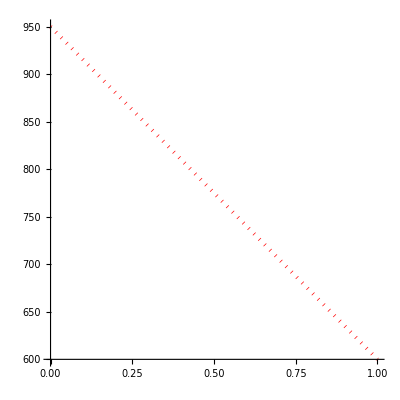

```mathematica
Plot[x,{x,0,1},PlotRange->{{0,1},{600,950}},ImageSize->{400,400},AspectRatio->Full,Epilog->{Thickness@0.007,Red,Dotted,Thickness@0.007,Line[{{0,950},{1,600}}]}]
```